```mathematica
Needs["Screening`",NotebookDirectory[]<>"../packages/Screening.wl"]
Needs["Capture`",NotebookDirectory[]<>"../packages/Capture.wl"]
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
```

```mathematica
Pdict = Utilities`ReadIt["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\Out\\25_02_2026\\δDicts\\δDict_1_aDbya_1_fD_0.01_delta_-1_0.dat"];
```

```mathematica
Keys@Pdict["δtable"]
```

{{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα},{δ,rmax,NCE,NC,Γcap,Γevap,ΓcapE,ΓevapE,logτs,meD,mpD,βD,nD,v0,κ,fD,αDbyα}}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

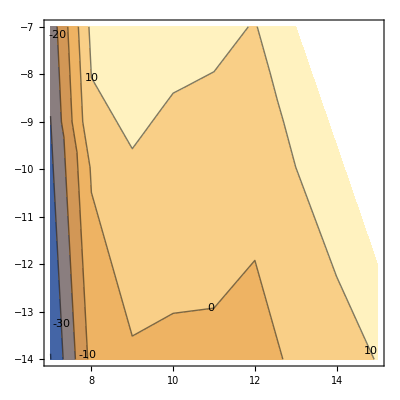

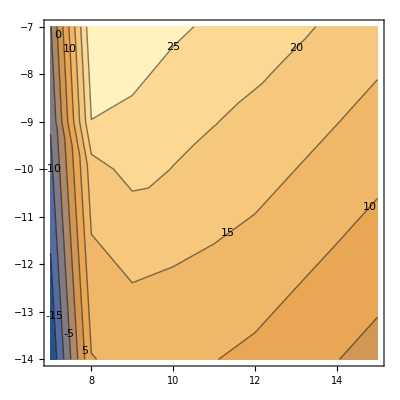

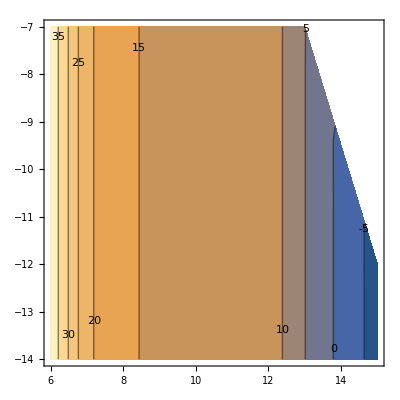

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

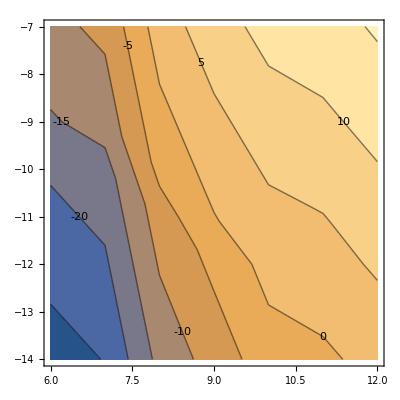

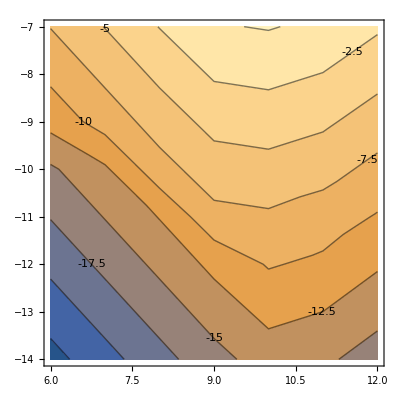

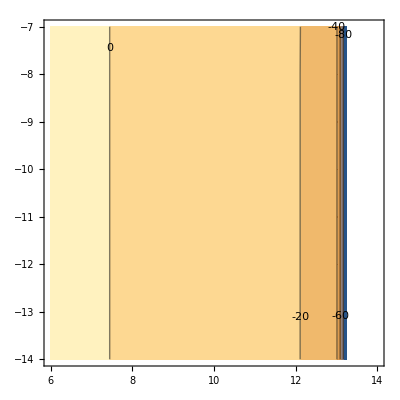

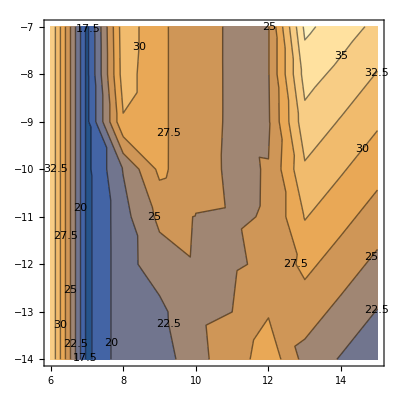

```mathematica
Log10@{"mpD"("c")^2/("JpereV"),"κ",("ΓcapE")/("Γcap"-"ΓcapE")}/.Pdict["δtable"]/.SIConstRepl;
ListContourPlot[%,ContourLabels->All]
Log10@{"mpD"("c")^2/("JpereV"),"κ","ΓcapE"}/.Pdict["δtable"]/.SIConstRepl;
ListContourPlot[%,ContourLabels->All]
Log10@{"mpD"("c")^2/("JpereV"),"κ","Γcap"-"ΓcapE"}/.Pdict["δtable"]/.SIConstRepl;
ListContourPlot[%,ContourLabels->All]
Log10@{"mpD"("c")^2/("JpereV"),"κ",("ΓevapE")/("Γevap"-"ΓevapE")}/.Pdict["δtable"]/.SIConstRepl;
ListContourPlot[%,ContourLabels->All]
Log10@{"mpD"("c")^2/("JpereV"),"κ","ΓevapE"}/.Pdict["δtable"]/.SIConstRepl;
ListContourPlot[%,ContourLabels->All]
Log10@{"mpD"("c")^2/("JpereV"),"κ","Γevap"-"ΓevapE"}/.Pdict["δtable"]/.SIConstRepl;
ListContourPlot[%,ContourLabels->All]
Log10@{"mpD"("c")^2/("JpereV"),"κ","NC"}/.Pdict["δtable"]/.SIConstRepl;
ListContourPlot[%,ContourLabels->All]
```

```mathematica
122.48 - 60.45
```

62.03